{{1.16747,-0.359036,1.10424},{-0.359036,0.378221,0.0586999},{1.10424,0.0586999,1.97974}}

## Circular

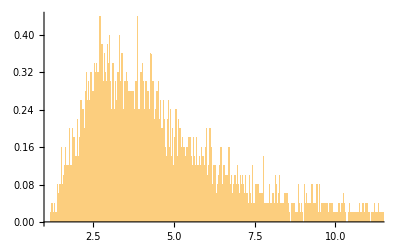

```mathematica
size=3;
Histogram[Table[Log@Sum[(A=RandomVariate[CircularRealMatrixDistribution[size]]^2)[[k,1]]/A[[k,m]],{k,1,Length@A},{m,1,Length@A}],{i,1,5000}],{0.01},"PDF"]
```

## Non-circular

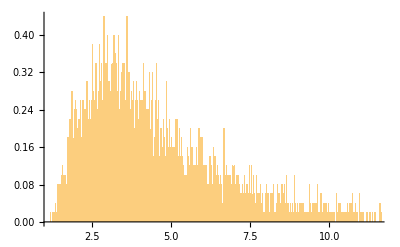

```mathematica
size=3;
Histogram[Table[Log@Sum[(A=Table[RandomVariate[CircularRealMatrixDistribution[size]][[i]],{i,1,size}]^2)[[k,1]]/A[[k,m]],{k,1,Length@A},{m,1,Length@A}],{i,1,5000}],{0.01},"PDF"]
```

## Non-square non-circular

To pierwsze jest poprawne, prawdopodobieństwa stanów początkowych są znormalizowane

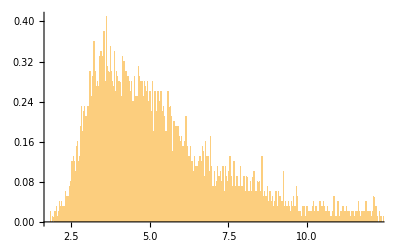

```mathematica
initial =5;
final =3;
Histogram[Table[Log@Sum[(A=Transpose[Table[RandomVariate[CircularRealMatrixDistribution[initial]][[1]],{i,1,final}]^2])[[k,1]]/A[[k,m]],{k,1,initial},{m,1,final}],{i,1,10000}],{0.01},"PDF"]
```

A nie prawdopodobieństwa stanów końcowych, jak poniżej

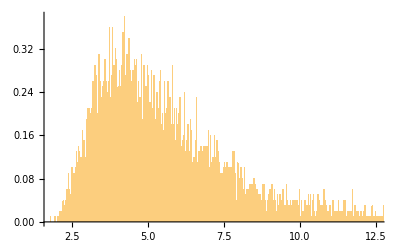

```mathematica
initial =5;
final =3;
Histogram[Table[Log@Sum[(A=Table[RandomVariate[CircularRealMatrixDistribution[final]][[1]],{i,1,initial}]^2)[[k,1]]/A[[k,m]],{k,1,initial},{m,1,final}],{i,1,10000}],{0.01},"PDF"]
```

# Weźmy jeszcze więcej stanów początkowych

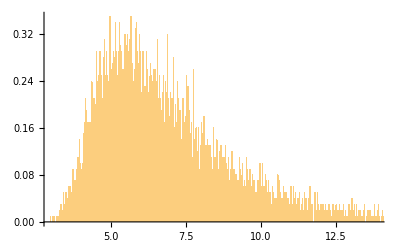

```mathematica
initial =10;
final =3;
Histogram[Table[Log@Sum[(A=Transpose[Table[RandomVariate[CircularRealMatrixDistribution[initial]][[1]],{i,1,final}]^2])[[k,1]]/A[[k,m]],{k,1,initial},{m,1,final}],{i,1,10000}],{0.01},"PDF"]
```

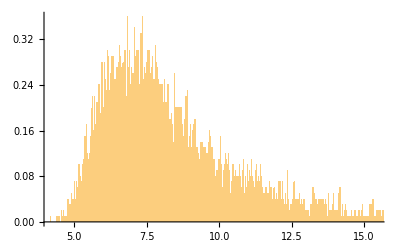

```mathematica
initial =20;
final =3;
Histogram[Table[Log@Sum[(A=Transpose[Table[RandomVariate[CircularRealMatrixDistribution[initial]][[1]],{i,1,final}]^2])[[k,1]]/A[[k,m]],{k,1,initial},{m,1,final}],{i,1,10000}],{0.01},"PDF"]
```

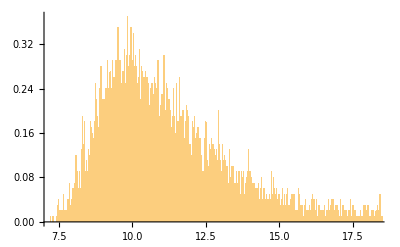

```mathematica
initial =20;
final =10;
Histogram[Table[Log@Sum[(A=Transpose[Table[RandomVariate[CircularRealMatrixDistribution[initial]][[1]],{i,1,final}]^2])[[k,1]]/A[[k,m]],{k,1,initial},{m,1,final}],{i,1,10000}],{0.01},"PDF"]
```